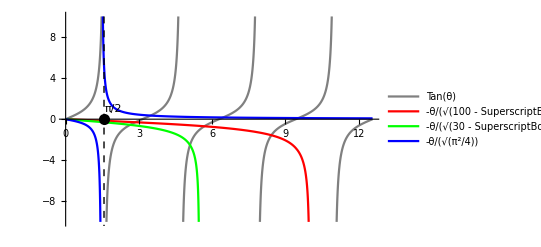

```mathematica
fig1=Plot[{Tan[θ],-θ/(√(100-θ^2)),-θ/(√(30-θ^2)),-θ/(Pi^2/4-0.3-θ^2)},{θ,0,4Pi},PlotLegends->{"Tan(θ)","-θ/(√(100 - SuperscriptBox[θ, 2]))","-θ/(√(30 - SuperscriptBox[θ, 2]))","-θ/(√(π^2/4))"},
	PlotStyle->{Gray,Red,Green,Blue},PlotRange->{Automatic,{-10,10}},Epilog->{Dashed,Black,Line[{{Pi/2,10},{Pi/2,-20}}],PointSize[0.02],Point[{Pi/2,0}],Text[π/2,{Pi/2+0.4,1}]}]
```

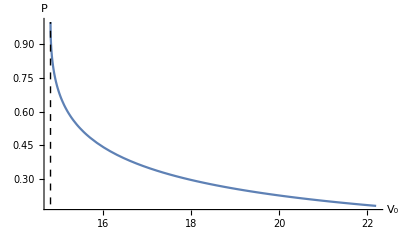

```mathematica
c=(6π^2)/4;
fig2=Plot[c/(x(1+√(x-c))),{x,c,(9π^2)/4},Epilog->{Dashed,Line[{{c,0},{c,1}}],PointSize[0.02],Point[{c,0}],Text[Style["c",Medium],{c+0.15,0.04}]},AxesOrigin->{c-1,0},AxesLabel->{"V_0","P"},PlotRange->All]
```

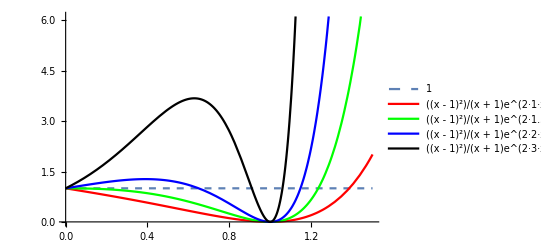

```mathematica
a1=1;a2=1.5;a3=2;a4=3;
fig3=Plot[{1,(x-1)^2/(x+1)Exp[2a1*x],(x-1)^2/(x+1)Exp[2a2*x],(x-1)^2/(x+1)Exp[2a3*x],(x-1)^2/(x+1)Exp[2a4*x]},{x,0,1.5},PlotLegends->{"1","(x - 1)^2/(x + 1)e^(2·1·x)","(x - 1)^2/(x + 1)e^(2·1.5·x)","(x - 1)^2/(x + 1)e^(2·2·x)","(x - 1)^2/(x + 1)e^(2·3·x)"},
		PlotStyle->{Dashed,Red,Green,Blue,Black}]
```

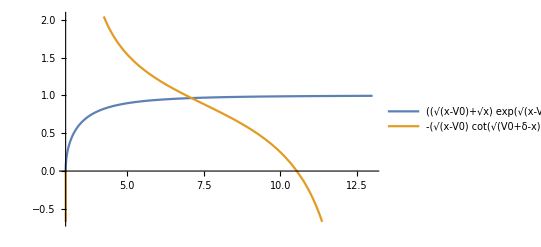

```mathematica
L=2;l=1;V0=3;δ=10;L=2;l=1;
Plot[{(((√(x-V0)+√x)Exp[√(x-V0)*L])+((√(x-V0)-√x)Exp[√(x-V0)*l]))/(((√(x-V0)+√x)Exp[√(x-V0)*L])-((√(x-V0)-√x)Exp[√(x-V0)*l])),(-√(x-V0))/(√(V0+δ-x))*Cot[√(V0+δ-x)*l]},{x,V0,V0+δ},PlotLegends->"Expressions"]
```

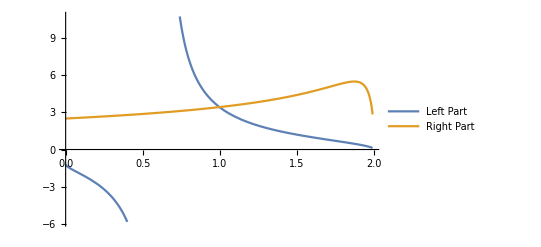

```mathematica
V0=2;δ=10;
fig4=Plot[{(√x*Tan[(√(V0-x))/2]+√(V0-x))/(√x-√(V0-x)*Tan[(√(V0-x))/2]),(-√(V0-x))/(√(V0+δ-x))*Tan[(√(V0+δ-x))/2]},{x,0,V0-0.01},PlotLegends->{"Left Part","Right Part"}]
```

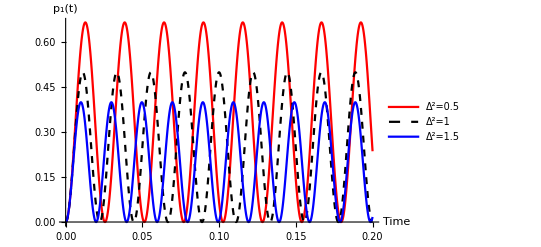

```mathematica
c=1;d1=0.5;k1=√(d1+c)/0.01;d2=1;k2=√(d2+c)/0.01;d3=1.5;k3=√(d3+c)/0.01;
fig2=Plot[{c/(d1+c)Sin[k1*x]^2,c/(d2+c)Sin[k2*x]^2,c/(d3+c)Sin[k3*x]^2},{x,0,0.2},PlotLegends->{"Δ^2=0.5","Δ^2=1","Δ^2=1.5"},PlotStyle->{Red,{Dashed,Black},Blue},AxesLabel->{"Time","p_1(t)"}]
```

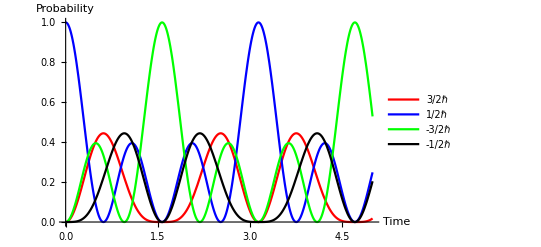

```mathematica
f1=Plot[{((√3)/4 Sin[3x]+(√3)/4 Sin[x])^2,(3/4 Cos[3x]+1/4 Cos[x])^2,(-3/4 Sin[3x]+1/4 Sin[x])^2,(-(√3)/4 Cos[3x]+(√3)/4 Cos[x])^2},{x,0,5},PlotLegends->{"3/2ℏ","1/2ℏ","-3/2ℏ","-1/2ℏ"},AxesLabel->{"Time","Probability"},PlotStyle->{Red,Blue,Green,Black}]
```

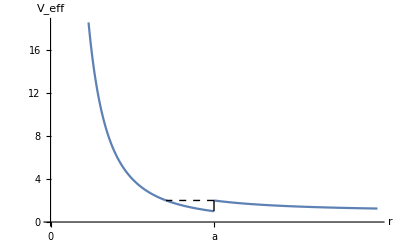

```mathematica
c=1;
f1=Plot[Piecewise[{{1/x^2,x<1},{1/x^2+c,x>1}}],{x,0,2},AxesLabel->{"r","V_eff"},Ticks->{{0,{1,"a"}},Automatic},Epilog->{{Dashed,Line[{{1,1+c},{1/(√(1+c)),1+c}}]}}];
f2=Graphics@Line[{{1,1},{1,1+c}}];
f3=Show[{f1,f2}]
```

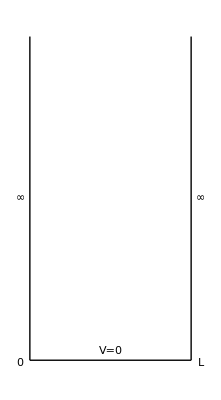

```mathematica
f2=Graphics[{{Thick,Line[{{0,0},{0.1,0}}]},{Thick,Line[{{0,0.2},{0,0}}]},{Thick,Line[{{0.1,0},{0.1,0.2}}]},Text[Style[0,Large],{-0.006,-0.002}],
	Text[Style["L",Large],{0.106,-0.002}],Text[Style["∞",Large],{0.106,0.1}],Text[Style["∞",Large],{-0.006,0.1}],Text[Style["V=0",Large],{0.05,0.006}]},Background->Automatic]
```

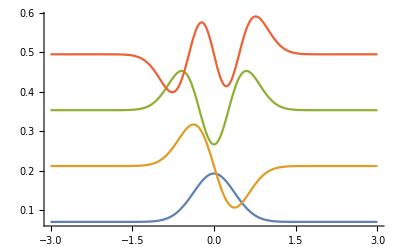

```mathematica
Clear["Global`*"]
h=1/10;V1[x_]:=Piecewise[{{1000,x<0},{1/2 x^2,x≥0}}];
V2[x_]:=1/2 x^2;
ℒ1=-h^2*u''[x]+V1[x]*u[x];
ℒ2=-h^2*u''[x]+V2[x]*u[x];
i=4;
{vals1,funs1}=NDEigensystem[ℒ1,u[x],{x,-3,3},i,Method->{"PDEDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.05}}}}];
{vals2,funs2}=NDEigensystem[ℒ2,u[x],{x,-3,3},i,Method->{"PDEDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.05}}}}];
Show[(*Plot[Evaluate[h*funs1+vals1],{x,-3,3},PlotRange->All,AxesOrigin->{0,0}]*)Plot[Evaluate[h*funs2+vals2],{x,-3,3},PlotRange->All,AxesOrigin->{0,0}]
]
```

```mathematica
Clear["Global`*"]
Schrodinger[{xmin_,xmax_},U_Function,NGrid_:101]:=Module[{dx=(xmax-xmin)/(NGrid-1),V`mat,T`mat,H`mat},
V`mat=DiagonalMatrix[U/@Range[xmin,xmax,dx]];
T`mat=DiagonalMatrix[Table[-1/(2(dx)^2)*(-2),NGrid]]+DiagonalMatrix[Table[-1/(2(dx)^2),NGrid-1],1]+DiagonalMatrix[Table[-1/(2(dx)^2),NGrid-1],-1];
H`mat=V`mat+T`mat;
Sort[Transpose[Eigensystem[N@H`mat]],#1[[1]]<#2[[1]]&]
];
Module[{},levels=2;fun1=1/2#^2&;
fun2=Piecewise[{{1000,#<0},{1/2#^2,#>=0}}]&;
fun3=Piecewise[{{0,#<-1},{-20,-1≤#≤1},{0,#>1}}]&;
fun4=1/2#^2+5Exp[-2#^2]&;]
Manipulate[pot`fun=Switch[d,1,fun1,2,fun2,3,fun3,4,fun4];sol=Schrodinger[{-10,10},pot`fun,2000];
eigenvalues=Transpose[sol][[1]];
eigenvecs=sol[[1;;-1,2]];
f1=ListLinePlot[Table[5eigenvecs[[i]]+eigenvalues[[i]],{i,levels}],PlotRange->{{-5,5},All},DataRange->{-10,10},Axes->False,Frame->True];
f2=ListLinePlot[Table[{x,pot`fun[x]},{x,-10,10,20/1000}],PlotRange->All];
Grid[{{Grid[Table[{Subscript["E", i],eigenvalues[[i]]},{i,levels}],Frame->All],Show[f1,f2,ImageSize->Medium]}}],{{d,1,"Potential Type"},{1,2,3,4}}]
```

Part::partd: Part specification Schrodinger[{-10,10},fun1,2000]⟦1;;-1,2⟧ is longer than depth of object.

Table::iterb: Iterator {i,levels} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Table[5. eigenvecs⟦i⟧+eigenvalues⟦i⟧,{i,levels}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Table[5 eigenvecs⟦i⟧+eigenvalues⟦i⟧,{i,levels}],PlotRange→{{-5,5},All},DataRange→{-10,10},Axes→False,Frame→True],,ImageSize→Medium].

Part::partd: Part specification Schrodinger[{-10,10},fun1,2000]⟦1;;-1,2⟧ is longer than depth of object.

Table::iterb: Iterator {i,levels} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Table[5. eigenvecs⟦i⟧+eigenvalues⟦i⟧,{i,levels}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Table[5 eigenvecs⟦i⟧+eigenvalues⟦i⟧,{i,levels}],PlotRange→{{-5,5},All},DataRange→{-10,10},Axes→False,Frame→True],,ImageSize→Medium].

Part::partd: Part specification Schrodinger[{-10,10},fun1,2000]⟦1;;-1,2⟧ is longer than depth of object.

Table::iterb: Iterator {i,levels} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Table[5. eigenvecs⟦i⟧+eigenvalues⟦i⟧,{i,levels}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Table[5 eigenvecs⟦i⟧+eigenvalues⟦i⟧,{i,levels}],PlotRange→{{-5,5},All},DataRange→{-10,10},Axes→False,Frame→True],,ImageSize→Medium].

Part::partd: Part specification Schrodinger[{-10,10},fun1,2000]⟦1;;-1,2⟧ is longer than depth of object.

Table::iterb: Iterator {i,levels} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Table[5. eigenvecs⟦i⟧+eigenvalues⟦i⟧,{i,levels}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Table[5 eigenvecs⟦i⟧+eigenvalues⟦i⟧,{i,levels}],PlotRange→{{-5,5},All},DataRange→{-10,10},Axes→False,Frame→True],,ImageSize→Medium].

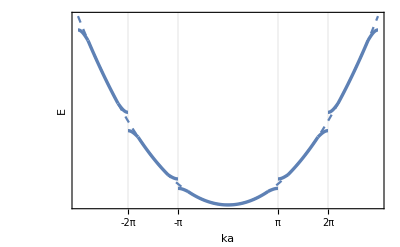

```mathematica
f1=Plot[x^2,{x,-6,6},PlotStyle->Dashed];
δ=0.4;
f2=Plot[Piecewise[{{x^2,-2+δ<=x<0},{(-2+δ)^2+ 0.6 Cos[(x+2)/(2δ)π],-2<x<-2+δ}}],{x,-2,0},PlotStyle->Thickness[0.006]];
f22=Plot[Piecewise[{{x^2,0<x<=2-δ},{(2-δ)^2+0.6 Cos[(x-2)/(2δ)π],2-δ<x<2}}],{x,0,2},PlotStyle->Thickness[0.006]];
f3=Plot[Piecewise[{{x^2,2+δ<x<4-δ},{(2+δ)^2- 0.8 Cos[(x-2)/(2δ)π],2<x<2+δ},{(4-δ)^2+ 1.2 Cos[(x-4)/(2δ)π],4-δ<x<4}}],{x,2,4},PlotStyle->Thickness[0.006]];
f33=Plot[Piecewise[{{x^2,-4+δ<x<-2-δ},{(-2-δ)^2-0.8 Cos[(x+2)/(2δ)π],-2-δ<x<-2},{(-4+δ)^2+1.2 Cos[(x+4)/(2δ)π],-4<x<-4+δ}}],{x,-2,-4},PlotStyle->Thickness[0.006]];
f4=Plot[Piecewise[{{x^2,4+δ<x<6-δ},{(4+δ)^2- 1.7 Cos[(x-4)/(2δ)π],4<x<4+δ},{(6-δ)^2+ 2 Cos[(x-6)/(2δ)π],6-δ<x<6}}],{x,4,6},PlotStyle->Thickness[0.006]];
f44=Plot[Piecewise[{{x^2,-6+δ<x<-4-δ},{(-4-δ)^2-1.7 Cos[(x+4)/(2δ)π],-4-δ<x<-4},{(-6+δ)^2+2 Cos[(x+6)/(2δ)π],-6<x<-6+δ}}],{x,-4,-6},PlotStyle->Thickness[0.006]];
(*f4=Plot[Piecewise[{{x^2,2+δ<x<3},{(2+δ)^2-0.6 Cos[(x-2)/(2δ)π],2<x<2+δ}}],{x,2,3},PlotStyle->Thickness[0.006]];*)
(*fig1=Show[{f1,f2,f3},Ticks->{{{-2,Text[Style["-nπ/a",6]]},{-2+δ,Text[Style["-nπ/a(1-δ)",6]]},{2,Text[Style["nπ/a",6]]},{2+δ,Text[Style["nπ/a(1+δ)",6]]}},None},
		Epilog->{{Dashed,Line[{{-2,0},{-2,(-2)^2}}]},{Dashed,Line[{{-2+0.6δ,0},{-2+0.6δ,(-2+0.6δ)^2}}]},
			{Dashed,Line[{{2+0.4δ,0},{2+0.4δ,(2+δ)^2-Abs[(2+0.4δ-2-δ)]^(0.5)}}]},{Dashed,Line[{{2,0},{2,(2)^2}}]}}]*)
fig2=Show[{f1,f2,f22,f3,f33,f4,f44},Frame->True,
	GridLines->Automatic,FrameTicks->{{None,None},{{{-2,Text[Style["-π",6]]},{2,Text[Style["π",6]]},{-4,Text[Style["-2π",6]]},{4,Text[Style["2π",6]]}},None}},FrameLabel->{"ka",Rotate[Text["E"],270°]}]
Clear["Global`*"]
```

```mathematica
Clear["Global`*"]
wl=25;w=1;T=Pi/2;dt=T/100;L=1;
point[t_]:=Evaluate[{L Sin[w t]Cos[wl t],L Sin[w t]Sin[wl t],L Cos[w t]}];
fig1[t_]:=Graphics3D[{{Red,Thick,Arrow[{{0,0,0},point[t]}]},{Blue,Sphere[point[t]/2,0.15]},
			Arrow[{{0,0,-1.2},{0,0,1.2}}],Arrow[{{-1.2,0,0},{1.2,0,0}}],Arrow[{{0,-1.2,0},{0,1.2,0}}]},Boxed->False,PlotRange->{{-1.2,1.2},{-1.2,1.2},{-0.2,1.2}},ViewPoint->{1,1,0.3}];
fig2[t_]:=ParametricPlot3D[Evaluate@point[t0],{t0,0,t},Boxed->False,Axes->False];
data=Table[Show[{fig1[t],fig2[t]}],{t,dt,T,dt}];
fd=Animate[Show[{fig1[t],fig2[t]}],{t,dt,T,dt}]
```

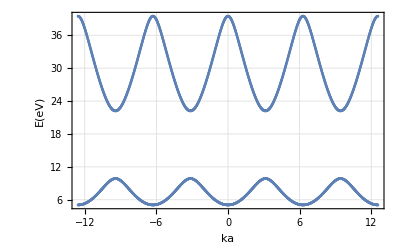

```mathematica
P=(3π)/2;a=1;
data=Table[Table[{x,y^2/.FindRoot[P/y Sin[y]+Cos[y]==Cos[x],{y,i}]},{x,-4π,4π,π/200}],{i,{1,5}}];
(*Length@data*)
newdata=Table[{data[[1]][[m]][[1]],data[[2]][[m]][[2]]-data[[1]][[m]][[2]]},{m,1,Length@data[[1]]}];
ListPlot[newdata,Frame->True];
fig=Table[ListPlot[data[[j]]],{j,1,Length@data}];
f1=Show[fig,PlotRange->All,AxesOrigin->{0,0},FrameLabel->{"ka","E(eV)"},Frame->True,GridLines->Automatic]
```